```mathematica
(* IMPORT MODULES *)
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
```

```mathematica
(* INITIALIZING PARAMETERS *)
uq=0.2848 (* up quark mass *);
sq=0.5553 (* strange quark mass *);
cq=1.8182 (* charm quark mass *);
bq=5.2019 (* bottom quark mass *);
sigma=0.154/2; (* coefficient of string strength term *)
alphaCoulomb=0; (* coefficient of Coulomb term (0.0175) if you want to replicate Bucks *)
Cqqq=-1.4204(* V = -Subscript[α, C]/r + σr + Subscript[C, qqq] *);
```

```mathematica
(* INITIALIZING HYPERPARAMETERS *)
γMax=6;
Λ=0;
m1=uq;
m2=uq;
m3=cq;
t1=tMatrix[Λ,γMax,1];
t2=tMatrix[Λ,γMax,2];
size=Dimensions[t1][[1]];
```

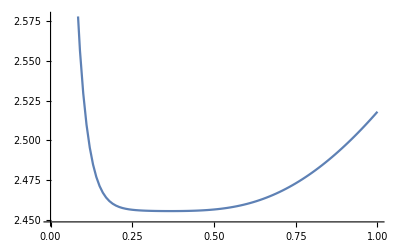

```mathematica
line=Table[{omega,Eigenvalues[baryonHamiltonian[omega]][[-1]]},{omega,0.01,1,0.01}];
ListPlot[line,Joined->True]
```

```mathematica
line3=line;
```

```mathematica
horizontal2=Table[{omega,2.455654361056725},{omega,0,1,0.01}];
```

```mathematica
x=ListPlot[{line1,line2,line3,horizontal2},Joined->True,
(*PlotLegends->{"N_Q=4","N_Q=10","N_Q=20"},*)
AxesLabel->{"ω [GeV]","Mass [GeV]"},
PlotStyle->{{Automatic,RGBColor[106/255,141/255,115/255]},{Automatic,RGBColor[78/255,81/255,102/255]},{Automatic,Brown},{Black,Dashed,Thin}},
LabelStyle->{FontSize->10,FontFamily->"Times",Black},
PlotLegends->Placed[{"N_Q=4","N_Q=10","N_Q=20","E_analytical"},{Center,Top}],
Prolog->{Lighter[Lighter[Lighter[Lighter[LightGray]]]],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}]
```

-Graphics-

```mathematica
Export["plots/eigenvalues/baryon_uuc.pdf",x,"PDF","AllowRasterization"->False]
```

plots/eigenvalues/baryon_uuc.pdf

```mathematica
expVal[omega_,s_]:=(
ω=omega;
vect=Eigenvectors[baryonHamiltonian[omega]][[-s]];
operator=polynomialOperatorRho[Λ,γMax,2];
exp=vect.operator.vect;
result=√(exp/α^2)/5.068
)
```

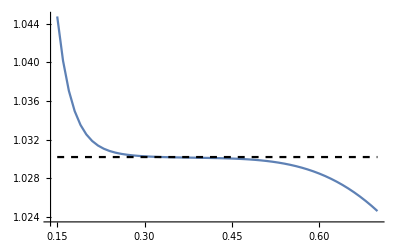

```mathematica
stableResult=expVal[0.33,1];
line2=Table[{omega,expVal[omega,1]},{omega,0.15,0.7,0.01}];
horizontal2=Table[{omega,stableResult},{omega,0.15,0.7,0.01}];
ListPlot[{line2,horizontal2},Joined->True,PlotStyle->{Automatic,{Black,Dashed}},PlotRange->All]
```

```mathematica
Export["lines/baryon_lines/expValues/rmsRho/uuc_1S1S_dim56.mx",line2]
```

lines/baryon_lines/expValues/rmsRho/uuc_1S1S_dim56.mx

```mathematica
Dimensions[stateMatrix[0,6]]
```

{20,20,2,4}

```mathematica
stableResult
```

1.03021

```mathematica
(Eigenvectors[baryonHamiltonian[0.29]][[-2]])^2//Chop
```

{0.000631471,0.919243,0,0.0148514,0.0434396,0,0.00104037,0.0120363,0,0.000639395,0.00589399,0,0.000276706,0,3.70991×10^-6,0,4.62242×10^-6,0.00181174,0,0.000127879}

```mathematica
stateMatrix[0,2]//MatrixForm
```

((0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1 | 0) | (0 | 0 | 0 | 0
0 | 1 | 0 | 1) | (0 | 0 | 0 | 0
1 | 0 | 0 | 0)
(0 | 0 | 1 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 1 | 0) | (0 | 0 | 1 | 0
0 | 1 | 0 | 1) | (0 | 0 | 1 | 0
1 | 0 | 0 | 0)
(0 | 1 | 0 | 1
0 | 0 | 0 | 0) | (0 | 1 | 0 | 1
0 | 0 | 1 | 0) | (0 | 1 | 0 | 1
0 | 1 | 0 | 1) | (0 | 1 | 0 | 1
1 | 0 | 0 | 0)
(1 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1 | 0 | 0 | 0
0 | 0 | 1 | 0) | (1 | 0 | 0 | 0
0 | 1 | 0 | 1) | (1 | 0 | 0 | 0
1 | 0 | 0 | 0))

```mathematica
(* THIS FUNCTION RETURNS THE BARYON HAMILTONIAN FOR A GIVEN ω *)
baryonHamiltonian[omega_]:=(
ω=omega;
vCoulomb=polynomialOperatorRho[Λ,γMax,-1];
vLinear=polynomialOperatorRho[Λ,γMax,1];
v12baryon=-alphaCoulomb*α*vCoulomb+(sigma*vLinear)/α;
v23baryon=-alphaCoulomb*α1*(Transpose[t1].vCoulomb.t1)+(sigma*(Transpose[t1].vLinear.t1))/α1;
v31baryon=-alphaCoulomb*α2*(Transpose[t2].vCoulomb.t2)+(sigma*(Transpose[t2].vLinear.t2))/α2;
kin=kMatrix[Λ,γMax,omega];
mas1=IdentityMatrix[size]*m1;
mas2=IdentityMatrix[size]*m2;
mas3=IdentityMatrix[size]*m3;
cqqq=IdentityMatrix[size]*(Cqqq);
Hbaryon=mas1+mas2+mas3+kin+v12baryon+v23baryon+v31baryon+cqqq)
```

```mathematica
(* THIS FUNCTION RETURNS THE BARYON HAMILTONIAN FOR A GIVEN ω *)
baryonHamiltonian2[omega_,γ_]:=(
ω=omega;
γMax=γ;
t1=tMatrix[Λ,γMax,1];
t2=tMatrix[Λ,γMax,2];
size=Dimensions[t1][[1]];
vCoulomb=polynomialOperatorRho[Λ,γMax,-1];
vLinear=polynomialOperatorRho[Λ,γMax,1];
v12baryon=-alphaCoulomb*α*vCoulomb+(sigma*vLinear)/α;
v23baryon=-alphaCoulomb*α1*(Transpose[t1].vCoulomb.t1)+(sigma*(Transpose[t1].vLinear.t1))/α1;
v31baryon=-alphaCoulomb*α2*(Transpose[t2].vCoulomb.t2)+(sigma*(Transpose[t2].vLinear.t2))/α2;
kin=kMatrix[Λ,γMax,omega];
mas1=IdentityMatrix[size]*m1;
mas2=IdentityMatrix[size]*m2;
mas3=IdentityMatrix[size]*m3;
cqqq=IdentityMatrix[size]*(Cqqq);
Hbaryon=mas1+mas2+mas3+kin+v12baryon+v23baryon+v31baryon+cqqq)
```

```mathematica
baryonHamiltonian2[1,6]//Dimensions
```

{20,20}

```mathematica
(* Optimises the lowest lying eigenvalue (searches for best ω) *)
baryonMinimumEigenvalue[gammaMax_,Lambda_,mass1_,mass2_,mass3_]:=(
γMax=gammaMax;
Λ=Lambda;
m1=mass1;
m2=mass2;
m3=mass3;
t1=tMatrix[Λ,gammaMax,1]; (* transformation matrix 1 *)
t2=tMatrix[Λ,gammaMax,2];(* transformation matrix 2 *)
size=Dimensions[t1][[1]]; (* size of matrix *)
Min[Table[Eigenvalues[baryonHamiltonian[ω]][[-1]],{ω,0.1,0.6,0.01}]])
```

```mathematica
baryonMinimumEigenvalue[6,0,m1,m2,m3]
```

2.45565

```mathematica
Eigenvalues[baryonHamiltonian[2.455654361056725]][[-2]]
```

5.07698

```mathematica
baryonList={{uq,uq,uq},{uq,uq,cq},{uq,uq,bq},{uq,sq,cq},{uq,sq,bq},{uq,cq,cq},{uq,cq,bq},{uq,bq,bq},{bq,cq,cq},{cq,cq,cq},{bq,bq,cq},{bq,bq,bq}};
```

```mathematica
For[index=1,index≤Length[baryonList],index++,
Print[index];
Print[baryonList[[index,1]]];
Print[baryonList[[index,2]]];
Print[baryonList[[index,3]]];
Print[Table[baryonMinimumEigenvalue[γMax,1,baryonList[[index,1]],baryonList[[index,2]],baryonList[[index,3]]],{γMax,1,7,2}]]]
```

1

0.2848

0.2848

0.2848

{1.49604,1.49527,1.49192,1.49182}

2

0.2848

0.2848

1.8182

{2.74812,2.72978,2.7255,2.72499}

3

0.2848

0.2848

5.2019

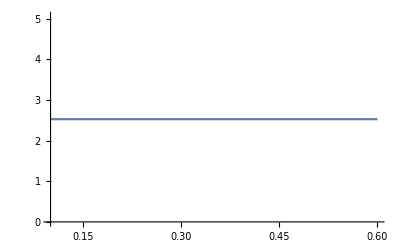

{{5.93237,0.1},{5.90381,0.11},{5.88171,0.12},{5.86459,0.13},{5.8513,0.14},{5.84101,0.15},{5.83305,0.16},{5.8269,0.17},{5.82215,0.18},{5.81851,0.19},{5.8157,0.2},{5.81355,0.21},{5.8119,0.22},{5.81062,0.23},{5.80964,0.24},{5.80889,0.25},{5.8083,0.26},{5.80784,0.27},{5.80749,0.28},{5.80721,0.29},{5.807,0.3},{5.80684,0.31},{5.80672,0.32},{5.80664,0.33},{5.80661,0.34},{5.8066,0.35},{5.80663,0.36},{5.8067,0.37},{5.80681,0.38},{5.80695,0.39},{5.80714,0.4},{5.80738,0.41},{5.80766,0.42},{5.808,0.43},{5.80839,0.44},{5.80884,0.45},{5.80935,0.46},{5.80992,0.47},{5.81055,0.48},{5.81125,0.49},{5.81202,0.5},{5.81286,0.51},{5.81377,0.52},{5.81476,0.53},{5.81582,0.54},{5.81695,0.55},{5.81816,0.56},{5.81944,0.57},{5.8208,0.58},{5.82224,0.59},{5.82375,0.6}}

```mathematica
Plot[Eigenvalues[baryonHamiltonian[ω]][[-1]],{ω,0.1,0.6}]
```